#### Theorie

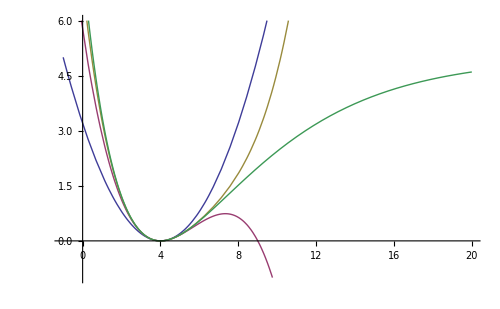

```mathematica
V=De(1-Exp[-a(r-re)])^2;
l={De->5,a->0.2,re->4};
Plot[{T2n/.l,T3n/.l,T4n/.l,V/.l},{r,-1,20},PlotRange->{-1,6},ImageSize->500]
```

```mathematica
T2=Series[V,{r,re,2}];
T2n=Normal[T2]
T3=Series[V,{r,re,3}];
T3n=Normal[T3]
T4=Series[V,{r,re,4}];
T4n=Normal[T4]
```

a^2 De (r-re)^2

a^2 De (r-re)^2-a^3 De (r-re)^3

a^2 De (r-re)^2-a^3 De (r-re)^3+7/12 a^4 De (r-re)^4

#### Anwendung

```mathematica
RepList={h->6.63*10^-34,c->3*10^8,M->0.5*126.9*1.66*10^-27,Be->2.9};
√(h/(2π 4 π c M Be))/.RepList
125*100*√((2π π c M)/(h 4392*100))/.RepList
```

3.02714×10^-10

1.82944×10^10

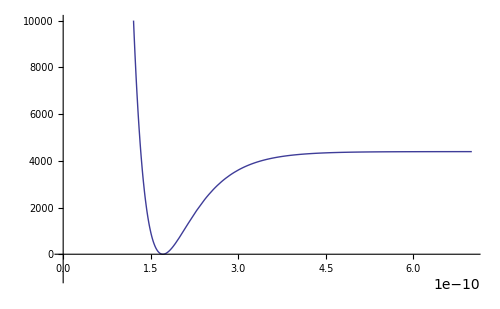

```mathematica
l={De->4392,a->125*100*√((2π π c M)/(h 4392*100))/.RepList,re->√(h/(π*2π 4 π c M Be))/.RepList};
Plot[{V/.l},{r,0,7*10^-10},PlotRange->{-1000,10000},ImageSize->500]
```